## Set your path to NonLinearSolver and get it

```mathematica
dddRicardo="/Users/ribeirrd/eclipse-workspace/MFGraphs/MFGraphs/NonLinearSolver.m";
```

```mathematica
Get[dddRicardo]
```

### DataToEquations and the critical congestion solver

```mathematica
Data=<|"Vertices List"->{1,2,3,4,5,6,7,8,9},"Adjacency Matrix"->{{0,0,1,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0},{0,0,0,0,1,0,0,0,0},{0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,1,1,1},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0}},"Entrance Vertices and Currents"->{{1,I1},{2,I2}},"Exit Vertices and Terminal Costs"->{{7,U1},{8,U2},{9,U3}},"Switching Costs"->{{5,6,7,1},{5,6,8,1},{5,6,9,1},{7,6,5,1},{7,6,8,1},{7,6,9,1},{8,6,5,1},{8,6,7,1},{8,6,9,1},{9,6,5,1},{9,6,7,1},{9,6,8,1}}|>;
d2e = Data2Equations[Data/.{I1->20,I2->10,U1->0,U2->0, U3->0}];
crit=CriticalCongestionSolver[d2e];//AbsoluteTiming
IsNonLinearSolution[crit]@crit["AssoCritical"]
crit=CriticalCongestionReduce[d2e];//AbsoluteTiming
IsNonLinearSolution[crit]@crit["AssoCritical"]
```

Iterative boolean convert took 0.079747 seconds to terminate

Iterative boolean convert took 9.×10^-6 seconds to terminate

{0.225808,Null}

All restrictions are True

Nrhs: {-16.033,-5.44452,-29.1456,-29.1456,-29.1456,-5.44452,-5.44452,-5.44452}
{-j1+j2-IntM[-j1+j2,1->3],-j3+j4-IntM[-j3+j4,2->3],-j5+j6-IntM[-j5+j6,3->4],-j7+j8-IntM[-j7+j8,4->5],j10-j9-IntM[j10-j9,5->6],-j11+j12-IntM[-j11+j12,6->7],-j13+j14-IntM[-j13+j14,6->8],-j15+j16-IntM[-j15+j16,6->9]}

Nlhs: {0.,0.,0.,0.,0.,0.,0.,0.}
{-j1+j2-u1+u2,-j3+j4-u3+u4,-j5+j6-u5+u6,-j7+j8-u7+u8,j10-j9+u10-u9,-j11+j12-u11+u12,-j13+j14-u13+u14,-j15+j16-u15+u16}

Max error for non-linear solution: 29.1456

<|u1→121.,u2→101.,u3→111.,u4→101.,u5→101.,u6→71.,u7→71.,u8→41.,u9→41.,u10→11.,u11→10.,u12→0.,u13→10.,u14→0.,u15→10.,u16→0.,u17→0.,u18→0.,u19→0.,u20→0.,u21→0.,u22→0.,u23→121.,u24→121.,u25→111.,u26→111.,j1→0.,j2→20.,j3→0.,j4→10.,j5→0.,j6→30.,j7→0.,j8→30.,j9→0.,j10→30.,j11→0.,j12→10.,j13→0.,j14→10.,j15→0.,j16→10.,j17→0.,j18→10.,j19→0.,j20→10.,j21→0.,j22→10.,j23→0.,j24→20.,j25→0.,j26→10.,jt1→0.,jt2→20.,jt3→0.,jt4→10.,jt5→0.,jt6→20.,jt7→0.,jt8→10.,jt9→0.,jt10→0.,jt11→30.,jt12→0.,jt13→30.,jt14→0.,jt15→10.,jt16→10.,jt17→10.,jt18→0.,jt19→0.,jt20→0.,jt21→0.,jt22→0.,jt23→0.,jt24→0.,jt25→0.,jt26→0.,jt27→10.,jt28→0.,jt29→10.,jt30→0.,jt31→10.,jt32→0.|>

Reducing jt15≥0&&jt16≥0&&jt15+jt16≤30&&u10≤1+u11&&1+u10≥u11&&u11≤jt15&&1000000+u11≥jt15&&u10≤1+u13&&1+u10≥u13&&u11≤1+u13&&1+u11≥u13&&u13≤jt16&&1000000+u13≥jt16&&u10≤1+u15&&1+u10≥u15&&u11≤1+u15&&1+u11≥u15&&u13≤1+u15&&1+u13≥u15&&jt15+jt16+u15≤30&&999970+jt15+jt16+u15≥0&&(jt15+jt16==30||jt15+jt16+u15==30)&&(jt15+jt16==30||u10==1+u15)&&(jt16==0||u10==1+u13)&&(jt15==0||u10==1+u11)&&(jt16==0||jt16==u13)&&(jt15==0||jt15==u11) ...

Reduce took 0.531325 seconds to terminate

Reducing True ...

Reduce took 0.000228 seconds to terminate

Reducing True ...

Reduce took 0.00023 seconds to terminate

{0.665782,Null}

All restrictions are True

Nrhs: {-16.033,-5.44452,-29.1456,-29.1456,-29.1456,-5.44452,-5.44452,-5.44452}
{-j1+j2-IntM[-j1+j2,1->3],-j3+j4-IntM[-j3+j4,2->3],-j5+j6-IntM[-j5+j6,3->4],-j7+j8-IntM[-j7+j8,4->5],j10-j9-IntM[j10-j9,5->6],-j11+j12-IntM[-j11+j12,6->7],-j13+j14-IntM[-j13+j14,6->8],-j15+j16-IntM[-j15+j16,6->9]}

Nlhs: {0.,0.,0.,0.,0.,0.,0.,0.}
{-j1+j2-u1+u2,-j3+j4-u3+u4,-j5+j6-u5+u6,-j7+j8-u7+u8,j10-j9+u10-u9,-j11+j12-u11+u12,-j13+j14-u13+u14,-j15+j16-u15+u16}

Max error for non-linear solution: 29.1456

<|u1→121.,u2→101.,u3→111.,u4→101.,u5→101.,u6→71.,u7→71.,u8→41.,u9→41.,u10→11.,u11→10.,u12→0.,u13→10.,u14→0.,u15→10.,u16→0.,u17→0.,u18→0.,u19→0.,u20→0.,u21→0.,u22→0.,u23→121.,u24→121.,u25→111.,u26→111.,j1→0.,j2→20.,j3→0.,j4→10.,j5→0.,j6→30.,j7→0.,j8→30.,j9→0.,j10→30.,j11→0.,j12→10.,j13→0.,j14→10.,j15→0.,j16→10.,j17→0.,j18→10.,j19→0.,j20→10.,j21→0.,j22→10.,j23→0.,j24→20.,j25→0.,j26→10.,jt1→0.,jt2→20.,jt3→0.,jt4→10.,jt5→0.,jt6→20.,jt7→0.,jt8→10.,jt9→0.,jt10→0.,jt11→30.,jt12→0.,jt13→30.,jt14→0.,jt15→10.,jt16→10.,jt17→10.,jt18→0.,jt19→0.,jt20→0.,jt21→0.,jt22→0.,jt23→0.,jt24→0.,jt25→0.,jt26→0.,jt27→10.,jt28→0.,jt29→10.,jt30→0.,jt31→10.,jt32→0.|>

```mathematica
%191[[1]]/%189[[1]]
```

47.4651

Don’t worry about the last 3 printed terms when checking for the critical congestion case.

```mathematica
IsNonLinearSolution[crit]@crit["AssoCritical"]
```

All restrictions are True

Nrhs: {-401.066,-401.066,-1002.32,-1002.32,-1002.32,-232.851,-232.851,-232.851}
{-j1+j2-IntM[-j1+j2,1->3],-j3+j4-IntM[-j3+j4,2->3],-j5+j6-IntM[-j5+j6,3->4],-j7+j8-IntM[-j7+j8,4->5],j10-j9-IntM[j10-j9,5->6],-j11+j12-IntM[-j11+j12,6->7],-j13+j14-IntM[-j13+j14,6->8],-j15+j16-IntM[-j15+j16,6->9]}

Nlhs: {0.,0.,0.,0.,0.,0.,0.,0.}
{-j1+j2-u1+u2,-j3+j4-u3+u4,-j5+j6-u5+u6,-j7+j8-u7+u8,j10-j9+u10-u9,-j11+j12-u11+u12,-j13+j14-u13+u14,-j15+j16-u15+u16}

Max error for non-linear solution: 1002.32

<|u1→1534.33,u2→1334.33,u3→1534.33,u4→1334.33,u5→1334.33,u6→934.333,u7→934.333,u8→534.333,u9→534.333,u10→134.333,u11→133.333,u12→0.,u13→133.333,u14→0.,u15→133.333,u16→0.,u17→0.,u18→0.,u19→0.,u20→0.,u21→0.,u22→0.,u23→1534.33,u24→1534.33,u25→1534.33,u26→1534.33,j1→0.,j2→200.,j3→0.,j4→200.,j5→0.,j6→400.,j7→0.,j8→400.,j9→0.,j10→400.,j11→0.,j12→133.333,j13→0.,j14→133.333,j15→0.,j16→133.333,j17→0.,j18→133.333,j19→0.,j20→133.333,j21→0.,j22→133.333,j23→0.,j24→200.,j25→0.,j26→200.,jt1→0.,jt2→200.,jt3→0.,jt4→200.,jt5→0.,jt6→200.,jt7→0.,jt8→200.,jt9→0.,jt10→0.,jt11→400.,jt12→0.,jt13→400.,jt14→0.,jt15→133.333,jt16→133.333,jt17→133.333,jt18→0.,jt19→0.,jt20→0.,jt21→0.,jt22→0.,jt23→0.,jt24→0.,jt25→0.,jt26→0.,jt27→133.333,jt28→0.,jt29→133.333,jt30→0.,jt31→133.333,jt32→0.|>

```mathematica
IsNonLinearSolution[crit]@Join[crit["AssoCritical"],<|jt32->1|>]
```

At least one of the restrictions is False

EqEntryIn: True
j24==200&&j26==200

EqValueAuxiliaryEdges: True
u23==u24&&u25==u26&&u17==u18&&u19==u20&&u21==u22

EqCompCon: False
(jt1==0||1000000-u1+u24==0)&&(jt2==0||u1-u24==0)&&(jt3==0||1000000+u26-u3==0)&&(jt4==0||-u26+u3==0)&&(jt5==0||-u2+u4==0)&&(jt6==0||-u2+u5==0)&&(jt7==0||u2-u4==0)&&(jt8==0||-u4+u5==0)&&(jt9==0||u2-u5==0)&&(jt10==0||u4-u5==0)&&(jt11==0||-u6+u7==0)&&(jt12==0||u6-u7==0)&&(jt13==0||-u8+u9==0)&&(jt14==0||u8-u9==0)&&(jt15==0||1-u10+u11==0)&&(jt16==0||1-u10+u13==0)&&(jt17==0||1-u10+u15==0)&&(jt18==0||1+u10-u11==0)&&(jt19==0||1-u11+u13==0)&&(jt20==0||1-u11+u15==0)&&(jt21==0||1+u10-u13==0)&&(jt22==0||1+u11-u13==0)&&(jt23==0||1-u13+u15==0)&&(jt24==0||1+u10-u15==0)&&(jt25==0||1+u11-u15==0)&&(jt26==0||1+u13-u15==0)&&(jt27==0||-u12+u17==0)&&(jt28==0||1000000+u12-u17==0)&&(jt29==0||-u14+u19==0)&&(jt30==0||1000000+u14-u19==0)&&(jt31==0||-u16+u21==0)&&(jt32==0||1000000+u16-u21==0)

EqBalanceSplittingCurrents: False
j1==jt1&&j24==jt2&&j3==jt3&&j26==jt4&&j2==jt5+jt6&&j4==jt7+jt8&&j5==jt10+jt9&&j6==jt11&&j7==jt12&&j8==jt13&&j9==jt14&&j10==jt15+jt16+jt17&&j11==jt18+jt19+jt20&&j13==jt21+jt22+jt23&&j15==jt24+jt25+jt26&&j12==jt27&&j17==jt28&&j14==jt29&&j19==jt30&&j16==jt31&&j21==jt32

EqCurrentCompCon: True
(j1==0||j2==0)&&(j3==0||j4==0)&&(j5==0||j6==0)&&(j7==0||j8==0)&&(j9==0||j10==0)&&(j11==0||j12==0)&&(j13==0||j14==0)&&(j15==0||j16==0)&&(j17==0||j18==0)&&(j19==0||j20==0)&&(j21==0||j22==0)&&(j23==0||j24==0)&&(j25==0||j26==0)

EqTransitionCompCon: False
(jt1==0||jt2==0)&&(jt10==0||jt8==0)&&(jt11==0||jt12==0)&&(jt13==0||jt14==0)&&(jt15==0||jt18==0)&&(jt16==0||jt21==0)&&(jt17==0||jt24==0)&&(jt19==0||jt22==0)&&(jt20==0||jt25==0)&&(jt23==0||jt26==0)&&(jt27==0||jt28==0)&&(jt29==0||jt30==0)&&(jt3==0||jt4==0)&&(jt31==0||jt32==0)&&(jt5==0||jt7==0)&&(jt6==0||jt9==0)

EqPosJs: True
j1≥0&&j2≥0&&j3≥0&&j4≥0&&j5≥0&&j6≥0&&j7≥0&&j8≥0&&j9≥0&&j10≥0&&j11≥0&&j12≥0&&j13≥0&&j14≥0&&j15≥0&&j16≥0&&j17≥0&&j18≥0&&j19≥0&&j20≥0&&j21≥0&&j22≥0&&j23≥0&&j24≥0&&j25≥0&&j26≥0

EqPosJts: True
jt1≥0&&jt2≥0&&jt3≥0&&jt4≥0&&jt5≥0&&jt6≥0&&jt7≥0&&jt8≥0&&jt9≥0&&jt10≥0&&jt11≥0&&jt12≥0&&jt13≥0&&jt14≥0&&jt15≥0&&jt16≥0&&jt17≥0&&jt18≥0&&jt19≥0&&jt20≥0&&jt21≥0&&jt22≥0&&jt23≥0&&jt24≥0&&jt25≥0&&jt26≥0&&jt27≥0&&jt28≥0&&jt29≥0&&jt30≥0&&jt31≥0&&jt32≥0

EqSwitchingByVertex: True
u1≤1000000+u24&&u24≤u1&&u3≤1000000+u26&&u26≤u3&&u2≤u4&&u2≤u5&&u4≤u2&&u4≤u5&&u5≤u2&&u5≤u4&&u6≤u7&&u7≤u6&&u8≤u9&&u9≤u8&&u10≤1+u11&&u10≤1+u13&&u10≤1+u15&&u11≤1+u10&&u11≤1+u13&&u11≤1+u15&&u13≤1+u10&&u13≤1+u11&&u13≤1+u15&&u15≤1+u10&&u15≤1+u11&&u15≤1+u13&&u12≤u17&&u17≤1000000+u12&&u14≤u19&&u19≤1000000+u14&&u16≤u21&&u21≤1000000+u16

Nrhs: {-401.066,-401.066,-1002.32,-1002.32,-1002.32,-232.851,-232.851,-232.851}
{-j1+j2-IntM[-j1+j2,1->3],-j3+j4-IntM[-j3+j4,2->3],-j5+j6-IntM[-j5+j6,3->4],-j7+j8-IntM[-j7+j8,4->5],j10-j9-IntM[j10-j9,5->6],-j11+j12-IntM[-j11+j12,6->7],-j13+j14-IntM[-j13+j14,6->8],-j15+j16-IntM[-j15+j16,6->9]}

Nlhs: {0.,0.,0.,0.,0.,0.,0.,0.}
{-j1+j2-u1+u2,-j3+j4-u3+u4,-j5+j6-u5+u6,-j7+j8-u7+u8,j10-j9+u10-u9,-j11+j12-u11+u12,-j13+j14-u13+u14,-j15+j16-u15+u16}

Max error for non-linear solution: 1002.32

<|u1→1534.33,u2→1334.33,u3→1534.33,u4→1334.33,u5→1334.33,u6→934.333,u7→934.333,u8→534.333,u9→534.333,u10→134.333,u11→133.333,u12→0.,u13→133.333,u14→0.,u15→133.333,u16→0.,u17→0.,u18→0.,u19→0.,u20→0.,u21→0.,u22→0.,u23→1534.33,u24→1534.33,u25→1534.33,u26→1534.33,j1→0.,j2→200.,j3→0.,j4→200.,j5→0.,j6→400.,j7→0.,j8→400.,j9→0.,j10→400.,j11→0.,j12→133.333,j13→0.,j14→133.333,j15→0.,j16→133.333,j17→0.,j18→133.333,j19→0.,j20→133.333,j21→0.,j22→133.333,j23→0.,j24→200.,j25→0.,j26→200.,jt1→0.,jt2→200.,jt3→0.,jt4→200.,jt5→0.,jt6→200.,jt7→0.,jt8→200.,jt9→0.,jt10→0.,jt11→400.,jt12→0.,jt13→400.,jt14→0.,jt15→133.333,jt16→133.333,jt17→133.333,jt18→0.,jt19→0.,jt20→0.,jt21→0.,jt22→0.,jt23→0.,jt24→0.,jt25→0.,jt26→0.,jt27→133.333,jt28→0.,jt29→133.333,jt30→0.,jt31→133.333,jt32→1.|>

#### Non-critical congestion solver

#### Starting from the critical congestion solution

```mathematica
nn=NonLinear[crit];//AbsoluteTiming
IsNonLinearSolution[nn][nn["AssoNonCritical"]];
```

Iterative boolean convert took 0.157919 seconds to terminate

Iterative boolean convert took 0.000013 seconds to terminate

Max error for non-linear solution: 9.5629

Iterative boolean convert took 0.161633 seconds to terminate

Iterative boolean convert took 0.000013 seconds to terminate

Max error for non-linear solution: 8.44864

Iterative boolean convert took 0.125125 seconds to terminate

Iterative boolean convert took 0.000011 seconds to terminate

Max error for non-linear solution: 8.05254

Iterative boolean convert took 0.171841 seconds to terminate

Iterative boolean convert took 9.×10^-6 seconds to terminate

Max error for non-linear solution: 7.67809

Iterative boolean convert took 0.140388 seconds to terminate

Iterative boolean convert took 0.000014 seconds to terminate

Max error for non-linear solution: 7.45628

Iterative boolean convert took 0.160558 seconds to terminate

Iterative boolean convert took 0.000013 seconds to terminate

Max error for non-linear solution: 7.25136

Iterative boolean convert took 0.139925 seconds to terminate

Iterative boolean convert took 0.000042 seconds to terminate

Max error for non-linear solution: 7.11234

Iterative boolean convert took 0.137907 seconds to terminate

Iterative boolean convert took 9.×10^-6 seconds to terminate

Max error for non-linear solution: 6.98011

Iterative boolean convert took 0.145197 seconds to terminate

Iterative boolean convert took 0.000011 seconds to terminate

Max error for non-linear solution: 6.88256

Iterative boolean convert took 0.21664 seconds to terminate

Iterative boolean convert took 0.000012 seconds to terminate

Max error for non-linear solution: 6.7851

Iterative boolean convert took 0.173696 seconds to terminate

Iterative boolean convert took 0.000017 seconds to terminate

Max error for non-linear solution: 6.70888

Iterative boolean convert took 0.159424 seconds to terminate

Iterative boolean convert took 0.000016 seconds to terminate

Max error for non-linear solution: 6.62915

Iterative boolean convert took 0.294864 seconds to terminate

Iterative boolean convert took 0.000016 seconds to terminate

Max error for non-linear solution: 6.56428

Iterative boolean convert took 0.142775 seconds to terminate

Iterative boolean convert took 0.00001 seconds to terminate

Max error for non-linear solution: 6.4942

Iterative boolean convert took 0.138261 seconds to terminate

Iterative boolean convert took 0.000011 seconds to terminate

Max error for non-linear solution: 6.43573

Iterated 15 times out of 15

{8.86706,Null}

All restrictions are True

Nrhs: {-16.033,-5.44452,-29.1456,-29.1456,-29.1456,-7.5241,-7.885,-1.72556}
{-j1+j2-IntM[-j1+j2,1->3],-j3+j4-IntM[-j3+j4,2->3],-j5+j6-IntM[-j5+j6,3->4],-j7+j8-IntM[-j7+j8,4->5],j10-j9-IntM[j10-j9,5->6],-j11+j12-IntM[-j11+j12,6->7],-j13+j14-IntM[-j13+j14,6->8],-j15+j16-IntM[-j15+j16,6->9]}

Nlhs: {-16.033,-5.44452,-29.1456,-29.1456,-29.1456,-13.9598,-3.5918,-1.02181}
{-j1+j2-u1+u2,-j3+j4-u3+u4,-j5+j6-u5+u6,-j7+j8-u7+u8,j10-j9+u10-u9,-j11+j12-u11+u12,-j13+j14-u13+u14,-j15+j16-u15+u16}

Max error for non-linear solution: 6.43573

```mathematica
nn2=NonLinear[nn];//AbsoluteTiming
```

Iterative boolean convert took 0.158207 seconds to terminate

Iterative boolean convert took 0.000011 seconds to terminate

Max error for non-linear solution: 6.37134

Iterative boolean convert took 0.15773 seconds to terminate

Iterative boolean convert took 0.000015 seconds to terminate

Max error for non-linear solution: 6.31679

Iterative boolean convert took 0.141005 seconds to terminate

Iterative boolean convert took 0.000016 seconds to terminate

Max error for non-linear solution: 6.25611

Iterative boolean convert took 0.18314 seconds to terminate

Iterative boolean convert took 0.000018 seconds to terminate

Max error for non-linear solution: 6.20422

Iterative boolean convert took 0.145373 seconds to terminate

Iterative boolean convert took 0.000029 seconds to terminate

Max error for non-linear solution: 6.14624

Iterative boolean convert took 0.341166 seconds to terminate

Iterative boolean convert took 0.000013 seconds to terminate

Max error for non-linear solution: 6.09634

Iterative boolean convert took 0.173521 seconds to terminate

Iterative boolean convert took 0.000029 seconds to terminate

Max error for non-linear solution: 6.04051

Iterative boolean convert took 0.158686 seconds to terminate

Iterative boolean convert took 9.×10^-6 seconds to terminate

Max error for non-linear solution: 5.99226

Iterative boolean convert took 0.132283 seconds to terminate

Iterative boolean convert took 0.000013 seconds to terminate

Max error for non-linear solution: 5.93828

Iterative boolean convert took 0.16589 seconds to terminate

Iterative boolean convert took 0.000014 seconds to terminate

Max error for non-linear solution: 5.89145

Iterative boolean convert took 0.149886 seconds to terminate

Iterative boolean convert took 0.000015 seconds to terminate

Max error for non-linear solution: 5.83913

Iterative boolean convert took 0.152454 seconds to terminate

Iterative boolean convert took 0.000015 seconds to terminate

Max error for non-linear solution: 5.79361

Iterative boolean convert took 0.20214 seconds to terminate

Iterative boolean convert took 0.000011 seconds to terminate

Max error for non-linear solution: 5.74282

Iterative boolean convert took 0.229274 seconds to terminate

Iterative boolean convert took 0.000012 seconds to terminate

Max error for non-linear solution: 5.69851

Iterative boolean convert took 0.164976 seconds to terminate

Iterative boolean convert took 0.000012 seconds to terminate

Max error for non-linear solution: 5.64915

Iterated 15 times out of 15

{8.85885,Null}

```mathematica
nn2=NonLinear[nn2];
```

Iterative boolean convert took 0.166666 seconds to terminate

Iterative boolean convert took 8.×10^-6 seconds to terminate

Max error for non-linear solution: 5.60599

Iterative boolean convert took 0.152229 seconds to terminate

Iterative boolean convert took 0.000048 seconds to terminate

Max error for non-linear solution: 5.55798

Iterative boolean convert took 0.123533 seconds to terminate

Iterative boolean convert took 0.00001 seconds to terminate

Max error for non-linear solution: 5.5159

Iterative boolean convert took 0.127628 seconds to terminate

Iterative boolean convert took 0.000013 seconds to terminate

Max error for non-linear solution: 5.46918

Iterative boolean convert took 0.140367 seconds to terminate

Iterative boolean convert took 0.000011 seconds to terminate

Max error for non-linear solution: 5.42814

Iterative boolean convert took 0.158676 seconds to terminate

Iterative boolean convert took 0.000016 seconds to terminate

Max error for non-linear solution: 5.38264

Iterative boolean convert took 0.12388 seconds to terminate

Iterative boolean convert took 0.000014 seconds to terminate

Max error for non-linear solution: 5.34259

Iterative boolean convert took 0.142132 seconds to terminate

Iterative boolean convert took 0.00002 seconds to terminate

Max error for non-linear solution: 5.29827

Iterative boolean convert took 0.164734 seconds to terminate

Iterative boolean convert took 0.000012 seconds to terminate

Max error for non-linear solution: 5.25916

Iterative boolean convert took 0.12384 seconds to terminate

Iterative boolean convert took 0.000011 seconds to terminate

Max error for non-linear solution: 5.21596

Iterative boolean convert took 0.192397 seconds to terminate

Iterative boolean convert took 0.000023 seconds to terminate

Max error for non-linear solution: 5.17777

Iterative boolean convert took 0.129546 seconds to terminate

Iterative boolean convert took 0.000011 seconds to terminate

Max error for non-linear solution: 5.13564

Iterative boolean convert took 0.142767 seconds to terminate

Iterative boolean convert took 0.000016 seconds to terminate

Max error for non-linear solution: 5.09832

Iterative boolean convert took 0.137766 seconds to terminate

Iterative boolean convert took 0.00001 seconds to terminate

Max error for non-linear solution: 5.05722

Iterative boolean convert took 0.129015 seconds to terminate

Iterative boolean convert took 0.000011 seconds to terminate

Max error for non-linear solution: 5.02074

Iterated 15 times out of 15

```mathematica
nn2=NonLinear[nn2];
```

Iterative boolean convert took 0.152776 seconds to terminate

Iterative boolean convert took 0.000012 seconds to terminate

Max error for non-linear solution: 4.98063

Iterative boolean convert took 0.16486 seconds to terminate

Iterative boolean convert took 0.000012 seconds to terminate

Max error for non-linear solution: 4.94496

Iterative boolean convert took 0.150005 seconds to terminate

Iterative boolean convert took 0.000043 seconds to terminate

Max error for non-linear solution: 4.9058

Iterative boolean convert took 0.135976 seconds to terminate

Iterative boolean convert took 0.000014 seconds to terminate

Max error for non-linear solution: 4.87091

Iterative boolean convert took 0.16538 seconds to terminate

Iterative boolean convert took 0.000015 seconds to terminate

Max error for non-linear solution: 4.83265

Iterative boolean convert took 0.137427 seconds to terminate

Iterative boolean convert took 0.000016 seconds to terminate

Max error for non-linear solution: 4.79852

Iterative boolean convert took 0.131398 seconds to terminate

Iterative boolean convert took 0.000014 seconds to terminate

Max error for non-linear solution: 4.76114

Iterative boolean convert took 0.131835 seconds to terminate

Iterative boolean convert took 0.000014 seconds to terminate

Max error for non-linear solution: 4.72773

Iterative boolean convert took 0.141138 seconds to terminate

Iterative boolean convert took 0.000016 seconds to terminate

Max error for non-linear solution: 4.69119

Iterative boolean convert took 0.180866 seconds to terminate

Iterative boolean convert took 0.000066 seconds to terminate

Max error for non-linear solution: 4.65848

Iterative boolean convert took 0.145881 seconds to terminate

Iterative boolean convert took 0.000051 seconds to terminate

Max error for non-linear solution: 4.62275

Iterative boolean convert took 0.17066 seconds to terminate

Iterative boolean convert took 0.000011 seconds to terminate

Max error for non-linear solution: 4.59071

Iterative boolean convert took 0.143433 seconds to terminate

Iterative boolean convert took 9.×10^-6 seconds to terminate

Max error for non-linear solution: 4.55577

Iterative boolean convert took 0.196393 seconds to terminate

Iterative boolean convert took 0.000017 seconds to terminate

Max error for non-linear solution: 4.52439

Iterative boolean convert took 0.149568 seconds to terminate

Iterative boolean convert took 0.000012 seconds to terminate

Max error for non-linear solution: 4.4902

Iterated 15 times out of 15

```mathematica
nn2=NonLinear[nn2];
```

Iterative boolean convert took 0.181793 seconds to terminate

Iterative boolean convert took 0.000019 seconds to terminate

Max error for non-linear solution: 4.45944

Iterative boolean convert took 0.192343 seconds to terminate

Iterative boolean convert took 0.000011 seconds to terminate

Max error for non-linear solution: 4.42598

Iterative boolean convert took 0.173095 seconds to terminate

Iterative boolean convert took 0.000012 seconds to terminate

Max error for non-linear solution: 4.39584

Iterative boolean convert took 0.214382 seconds to terminate

Iterative boolean convert took 0.000012 seconds to terminate

Max error for non-linear solution: 4.36308

Iterative boolean convert took 0.184927 seconds to terminate

Iterative boolean convert took 0.000018 seconds to terminate

Max error for non-linear solution: 4.33353

Iterative boolean convert took 0.143133 seconds to terminate

Iterative boolean convert took 0.000018 seconds to terminate

Max error for non-linear solution: 4.30145

Iterative boolean convert took 0.168221 seconds to terminate

Iterative boolean convert took 0.000018 seconds to terminate

Max error for non-linear solution: 4.27247

Iterative boolean convert took 0.153684 seconds to terminate

Iterative boolean convert took 0.000014 seconds to terminate

Max error for non-linear solution: 4.24105

Iterative boolean convert took 0.143578 seconds to terminate

Iterative boolean convert took 0.000014 seconds to terminate

Max error for non-linear solution: 4.21262

Iterative boolean convert took 0.156144 seconds to terminate

Iterative boolean convert took 0.000015 seconds to terminate

Max error for non-linear solution: 4.18183

Iterative boolean convert took 0.150512 seconds to terminate

Iterative boolean convert took 0.000014 seconds to terminate

Max error for non-linear solution: 4.15394

Iterative boolean convert took 0.138573 seconds to terminate

Iterative boolean convert took 0.000021 seconds to terminate

Max error for non-linear solution: 4.12377

Iterative boolean convert took 0.168103 seconds to terminate

Iterative boolean convert took 0.000022 seconds to terminate

Max error for non-linear solution: 4.09639

Iterative boolean convert took 0.182449 seconds to terminate

Iterative boolean convert took 0.000015 seconds to terminate

Max error for non-linear solution: 4.06682

Iterative boolean convert took 0.150875 seconds to terminate

Iterative boolean convert took 0.000015 seconds to terminate

Max error for non-linear solution: 4.03995

Iterated 15 times out of 15

```mathematica
nn2=NonLinear[nn2];
```

Iterative boolean convert took 0.173352 seconds to terminate

Iterative boolean convert took 0.000017 seconds to terminate

Max error for non-linear solution: 4.01096

Iterative boolean convert took 0.199478 seconds to terminate

Iterative boolean convert took 9.×10^-6 seconds to terminate

Max error for non-linear solution: 3.98457

Iterative boolean convert took 0.168475 seconds to terminate

Iterative boolean convert took 0.00001 seconds to terminate

Max error for non-linear solution: 3.95614

Iterative boolean convert took 0.176735 seconds to terminate

Iterative boolean convert took 0.000021 seconds to terminate

Max error for non-linear solution: 3.93023

Iterative boolean convert took 0.19786 seconds to terminate

Iterative boolean convert took 0.000012 seconds to terminate

Max error for non-linear solution: 3.90234

Iterative boolean convert took 0.261241 seconds to terminate

Iterative boolean convert took 0.000027 seconds to terminate

Max error for non-linear solution: 3.8769

Iterative boolean convert took 0.193197 seconds to terminate

Iterative boolean convert took 0.000012 seconds to terminate

Max error for non-linear solution: 3.84953

Iterative boolean convert took 0.183665 seconds to terminate

Iterative boolean convert took 0.000017 seconds to terminate

Max error for non-linear solution: 3.82453

Iterative boolean convert took 0.152983 seconds to terminate

Iterative boolean convert took 0.000015 seconds to terminate

Max error for non-linear solution: 3.79768

Iterative boolean convert took 0.186811 seconds to terminate

Iterative boolean convert took 0.000012 seconds to terminate

Max error for non-linear solution: 3.77312

Iterative boolean convert took 0.153808 seconds to terminate

Iterative boolean convert took 0.000016 seconds to terminate

Max error for non-linear solution: 3.74676

Iterative boolean convert took 0.176443 seconds to terminate

Iterative boolean convert took 0.000015 seconds to terminate

Max error for non-linear solution: 3.72262

Iterative boolean convert took 0.148201 seconds to terminate

Iterative boolean convert took 0.000013 seconds to terminate

Max error for non-linear solution: 3.69675

Iterative boolean convert took 0.230577 seconds to terminate

Iterative boolean convert took 0.000016 seconds to terminate

Max error for non-linear solution: 3.67303

Iterative boolean convert took 0.181875 seconds to terminate

Iterative boolean convert took 0.000012 seconds to terminate

Max error for non-linear solution: 3.64762

Iterated 15 times out of 15

```mathematica
nn2=NonLinear[nn2];
```

Iterative boolean convert took 0.192445 seconds to terminate

Iterative boolean convert took 0.00003 seconds to terminate

Max error for non-linear solution: 3.6243

Iterative boolean convert took 0.154357 seconds to terminate

Iterative boolean convert took 0.000018 seconds to terminate

Max error for non-linear solution: 3.59934

Iterative boolean convert took 0.150545 seconds to terminate

Iterative boolean convert took 0.000026 seconds to terminate

Max error for non-linear solution: 3.57642

Iterative boolean convert took 0.164121 seconds to terminate

Iterative boolean convert took 0.000026 seconds to terminate

Max error for non-linear solution: 3.5519

Iterative boolean convert took 0.148128 seconds to terminate

Iterative boolean convert took 0.000014 seconds to terminate

Max error for non-linear solution: 3.52936

Iterative boolean convert took 0.231568 seconds to terminate

Iterative boolean convert took 0.000019 seconds to terminate

Max error for non-linear solution: 3.50528

Iterative boolean convert took 0.169855 seconds to terminate

Iterative boolean convert took 0.000012 seconds to terminate

Max error for non-linear solution: 3.48311

Iterative boolean convert took 0.176125 seconds to terminate

Iterative boolean convert took 0.000012 seconds to terminate

Max error for non-linear solution: 3.45944

Iterative boolean convert took 0.142321 seconds to terminate

Iterative boolean convert took 0.000017 seconds to terminate

Max error for non-linear solution: 3.43763

Iterative boolean convert took 0.164757 seconds to terminate

Iterative boolean convert took 0.00001 seconds to terminate

Max error for non-linear solution: 3.41438

Iterative boolean convert took 0.158128 seconds to terminate

Iterative boolean convert took 0.000012 seconds to terminate

Max error for non-linear solution: 3.39292

Iterative boolean convert took 0.203007 seconds to terminate

Iterative boolean convert took 0.000018 seconds to terminate

Max error for non-linear solution: 3.37007

Iterative boolean convert took 0.229483 seconds to terminate

Iterative boolean convert took 0.000019 seconds to terminate

Max error for non-linear solution: 3.34896

Iterative boolean convert took 0.15009 seconds to terminate

Iterative boolean convert took 0.000012 seconds to terminate

Max error for non-linear solution: 3.32649

Iterative boolean convert took 0.160499 seconds to terminate

Iterative boolean convert took 0.000016 seconds to terminate

Max error for non-linear solution: 3.30571

Iterated 15 times out of 15

```mathematica
nn2=NonLinear[nn2];
```

Iterative boolean convert took 0.154442 seconds to terminate

Iterative boolean convert took 9.×10^-6 seconds to terminate

Max error for non-linear solution: 3.28362

Iterative boolean convert took 0.16492 seconds to terminate

Iterative boolean convert took 0.000016 seconds to terminate

Max error for non-linear solution: 3.26318

Iterative boolean convert took 0.162898 seconds to terminate

Iterative boolean convert took 0.000011 seconds to terminate

Max error for non-linear solution: 3.24145

Iterative boolean convert took 0.152721 seconds to terminate

Iterative boolean convert took 0.000046 seconds to terminate

Max error for non-linear solution: 3.22133

Iterative boolean convert took 0.146051 seconds to terminate

Iterative boolean convert took 0.000016 seconds to terminate

Max error for non-linear solution: 3.19996

Iterative boolean convert took 0.150361 seconds to terminate

Iterative boolean convert took 0.000011 seconds to terminate

Max error for non-linear solution: 3.18015

Iterative boolean convert took 0.174116 seconds to terminate

Iterative boolean convert took 0.000015 seconds to terminate

Max error for non-linear solution: 3.15914

Iterative boolean convert took 0.201624 seconds to terminate

Iterative boolean convert took 0.00002 seconds to terminate

Max error for non-linear solution: 3.13963

Iterative boolean convert took 0.177341 seconds to terminate

Iterative boolean convert took 0.000012 seconds to terminate

Max error for non-linear solution: 3.11896

Iterative boolean convert took 0.153023 seconds to terminate

Iterative boolean convert took 0.000012 seconds to terminate

Max error for non-linear solution: 3.09976

Iterative boolean convert took 0.156496 seconds to terminate

Iterative boolean convert took 0.000011 seconds to terminate

Max error for non-linear solution: 3.07942

Iterative boolean convert took 0.170199 seconds to terminate

Iterative boolean convert took 0.000021 seconds to terminate

Max error for non-linear solution: 3.06051

Iterative boolean convert took 0.18659 seconds to terminate

Iterative boolean convert took 0.000015 seconds to terminate

Max error for non-linear solution: 3.04049

Iterative boolean convert took 0.150367 seconds to terminate

Iterative boolean convert took 0.000016 seconds to terminate

Max error for non-linear solution: 3.02187

Iterative boolean convert took 0.159603 seconds to terminate

Iterative boolean convert took 0.000017 seconds to terminate

Max error for non-linear solution: 3.00217

Iterated 15 times out of 15

```mathematica
nn2=FixedPoint[NonLinear,nn2,10];
```

Iterative boolean convert took 0.218629 seconds to terminate

Iterative boolean convert took 0.000956 seconds to terminate

Max error for non-linear solution: 2.98383

Iterative boolean convert took 0.179339 seconds to terminate

Iterative boolean convert took 0.000017 seconds to terminate

Max error for non-linear solution: 2.96444

Iterative boolean convert took 0.177979 seconds to terminate

Iterative boolean convert took 0.000014 seconds to terminate

Max error for non-linear solution: 2.94637

Iterative boolean convert took 0.137681 seconds to terminate

Iterative boolean convert took 0.000014 seconds to terminate

Max error for non-linear solution: 2.92729

Iterative boolean convert took 0.202007 seconds to terminate

Iterative boolean convert took 0.000014 seconds to terminate

Max error for non-linear solution: 2.90949

Iterative boolean convert took 0.151888 seconds to terminate

Iterative boolean convert took 0.000011 seconds to terminate

Max error for non-linear solution: 2.8907

Iterative boolean convert took 0.37116 seconds to terminate

Iterative boolean convert took 0.000015 seconds to terminate

Max error for non-linear solution: 2.87316

Iterative boolean convert took 0.194273 seconds to terminate

Iterative boolean convert took 0.000017 seconds to terminate

Max error for non-linear solution: 2.85467

Iterative boolean convert took 0.171957 seconds to terminate

Iterative boolean convert took 0.000015 seconds to terminate

Max error for non-linear solution: 2.83738

Iterative boolean convert took 0.154743 seconds to terminate

Iterative boolean convert took 9.×10^-6 seconds to terminate

Max error for non-linear solution: 2.81917

Iterative boolean convert took 0.252701 seconds to terminate

Iterative boolean convert took 0.000013 seconds to terminate

Max error for non-linear solution: 2.80214

Iterative boolean convert took 0.193725 seconds to terminate

Iterative boolean convert took 0.000015 seconds to terminate

Max error for non-linear solution: 2.78421

Iterative boolean convert took 0.217945 seconds to terminate

Iterative boolean convert took 0.000061 seconds to terminate

Max error for non-linear solution: 2.76743

Iterative boolean convert took 0.167329 seconds to terminate

Iterative boolean convert took 9.×10^-6 seconds to terminate

Max error for non-linear solution: 2.74976

Iterative boolean convert took 0.133407 seconds to terminate

Iterative boolean convert took 0.000011 seconds to terminate

Max error for non-linear solution: 2.73322

Iterated 15 times out of 15

Iterative boolean convert took 0.178236 seconds to terminate

Iterative boolean convert took 0.000015 seconds to terminate

Max error for non-linear solution: 2.71583

Iterative boolean convert took 0.161248 seconds to terminate

Iterative boolean convert took 9.×10^-6 seconds to terminate

Max error for non-linear solution: 2.69952

Iterative boolean convert took 0.62425 seconds to terminate

Iterative boolean convert took 0.000019 seconds to terminate

Max error for non-linear solution: 2.68238

Iterative boolean convert took 0.16629 seconds to terminate

Iterative boolean convert took 0.000014 seconds to terminate

Max error for non-linear solution: 2.66631

Iterative boolean convert took 0.22094 seconds to terminate

Iterative boolean convert took 0.000026 seconds to terminate

Max error for non-linear solution: 2.64943

Iterative boolean convert took 0.286772 seconds to terminate

Iterative boolean convert took 0.000016 seconds to terminate

Max error for non-linear solution: 2.63358

Iterative boolean convert took 0.345219 seconds to terminate

Iterative boolean convert took 0.000013 seconds to terminate

Max error for non-linear solution: 2.61695

Iterative boolean convert took 0.196876 seconds to terminate

Iterative boolean convert took 0.000021 seconds to terminate

Max error for non-linear solution: 2.60133

Iterative boolean convert took 0.211929 seconds to terminate

Iterative boolean convert took 0.00002 seconds to terminate

Max error for non-linear solution: 2.58494

Iterative boolean convert took 0.21385 seconds to terminate

Iterative boolean convert took 0.000012 seconds to terminate

Max error for non-linear solution: 2.56954

Iterative boolean convert took 0.193324 seconds to terminate

Iterative boolean convert took 0.000014 seconds to terminate

Max error for non-linear solution: 2.55339

Iterative boolean convert took 0.143659 seconds to terminate

Iterative boolean convert took 0.000014 seconds to terminate

Max error for non-linear solution: 2.5382

Iterative boolean convert took 0.176136 seconds to terminate

Iterative boolean convert took 0.000013 seconds to terminate

Max error for non-linear solution: 2.52229

Iterative boolean convert took 0.15125 seconds to terminate

Iterative boolean convert took 0.000011 seconds to terminate

Max error for non-linear solution: 2.50731

Iterative boolean convert took 0.186371 seconds to terminate

Iterative boolean convert took 0.000012 seconds to terminate

Max error for non-linear solution: 2.49163

Iterated 15 times out of 15

Iterative boolean convert took 0.143742 seconds to terminate

Iterative boolean convert took 0.000024 seconds to terminate

Max error for non-linear solution: 2.47685

Iterative boolean convert took 0.178735 seconds to terminate

Iterative boolean convert took 9.×10^-6 seconds to terminate

Max error for non-linear solution: 2.4614

Iterative boolean convert took 0.149703 seconds to terminate

Iterative boolean convert took 0.00002 seconds to terminate

Max error for non-linear solution: 2.44683

Iterative boolean convert took 0.170944 seconds to terminate

Iterative boolean convert took 0.000017 seconds to terminate

Max error for non-linear solution: 2.43159

Iterative boolean convert took 0.165019 seconds to terminate

Iterative boolean convert took 0.000012 seconds to terminate

Max error for non-linear solution: 2.41722

Iterative boolean convert took 0.160776 seconds to terminate

Iterative boolean convert took 0.000017 seconds to terminate

Max error for non-linear solution: 2.4022

Iterative boolean convert took 0.164206 seconds to terminate

Iterative boolean convert took 0.000017 seconds to terminate

Max error for non-linear solution: 2.38803

Iterative boolean convert took 0.182665 seconds to terminate

Iterative boolean convert took 0.000014 seconds to terminate

Max error for non-linear solution: 2.37322

Iterative boolean convert took 0.226777 seconds to terminate

Iterative boolean convert took 0.000016 seconds to terminate

Max error for non-linear solution: 2.35924

Iterative boolean convert took 0.261774 seconds to terminate

Iterative boolean convert took 0.000013 seconds to terminate

Max error for non-linear solution: 2.34464

Iterative boolean convert took 0.171867 seconds to terminate

Iterative boolean convert took 0.000012 seconds to terminate

Max error for non-linear solution: 2.33085

Iterative boolean convert took 0.321386 seconds to terminate

Iterative boolean convert took 0.00002 seconds to terminate

Max error for non-linear solution: 2.31646

Iterative boolean convert took 0.140584 seconds to terminate

Iterative boolean convert took 0.000013 seconds to terminate

Max error for non-linear solution: 2.30284

Iterative boolean convert took 0.163048 seconds to terminate

Iterative boolean convert took 0.000013 seconds to terminate

Max error for non-linear solution: 2.28865

Iterative boolean convert took 0.172316 seconds to terminate

Iterative boolean convert took 0.000022 seconds to terminate

Max error for non-linear solution: 2.27522

Iterated 15 times out of 15

Iterative boolean convert took 0.234215 seconds to terminate

Iterative boolean convert took 0.000018 seconds to terminate

Max error for non-linear solution: 2.26123

Iterative boolean convert took 0.157837 seconds to terminate

Iterative boolean convert took 0.000019 seconds to terminate

Max error for non-linear solution: 2.24798

Iterative boolean convert took 0.149347 seconds to terminate

Iterative boolean convert took 0.000019 seconds to terminate

Max error for non-linear solution: 2.23418

Iterative boolean convert took 0.16549 seconds to terminate

Iterative boolean convert took 0.000013 seconds to terminate

Max error for non-linear solution: 2.22111

Iterative boolean convert took 0.154858 seconds to terminate

Iterative boolean convert took 0.000016 seconds to terminate

Max error for non-linear solution: 2.2075

Iterative boolean convert took 0.179641 seconds to terminate

Iterative boolean convert took 0.00001 seconds to terminate

Max error for non-linear solution: 2.19459

Iterative boolean convert took 0.170675 seconds to terminate

Iterative boolean convert took 0.000016 seconds to terminate

Max error for non-linear solution: 2.18117

Iterative boolean convert took 0.154287 seconds to terminate

Iterative boolean convert took 0.000012 seconds to terminate

Max error for non-linear solution: 2.16844

Iterative boolean convert took 0.156065 seconds to terminate

Iterative boolean convert took 0.000015 seconds to terminate

Max error for non-linear solution: 2.1552

Iterative boolean convert took 0.17217 seconds to terminate

Iterative boolean convert took 0.000014 seconds to terminate

Max error for non-linear solution: 2.14263

Iterative boolean convert took 0.192583 seconds to terminate

Iterative boolean convert took 0.000015 seconds to terminate

Max error for non-linear solution: 2.12957

Iterative boolean convert took 0.205734 seconds to terminate

Iterative boolean convert took 0.000026 seconds to terminate

Max error for non-linear solution: 2.11717

Iterative boolean convert took 0.187042 seconds to terminate

Iterative boolean convert took 0.000014 seconds to terminate

Max error for non-linear solution: 2.10429

Iterative boolean convert took 0.143122 seconds to terminate

Iterative boolean convert took 0.000012 seconds to terminate

Max error for non-linear solution: 2.09205

Iterative boolean convert took 0.151636 seconds to terminate

Iterative boolean convert took 0.000016 seconds to terminate

Max error for non-linear solution: 2.07934

Iterated 15 times out of 15

Iterative boolean convert took 0.161416 seconds to terminate

Iterative boolean convert took 0.000012 seconds to terminate

Max error for non-linear solution: 2.06726

Iterative boolean convert took 0.154116 seconds to terminate

Iterative boolean convert took 0.000016 seconds to terminate

Max error for non-linear solution: 2.05472

Iterative boolean convert took 0.22293 seconds to terminate

Iterative boolean convert took 0.00001 seconds to terminate

Max error for non-linear solution: 2.04279

Iterative boolean convert took 0.209759 seconds to terminate

Iterative boolean convert took 0.000016 seconds to terminate

Max error for non-linear solution: 2.03043

Iterative boolean convert took 0.158679 seconds to terminate

Iterative boolean convert took 0.000019 seconds to terminate

Max error for non-linear solution: 2.01865

Iterative boolean convert took 0.168234 seconds to terminate

Iterative boolean convert took 0.000012 seconds to terminate

Max error for non-linear solution: 2.00645

Iterative boolean convert took 0.208471 seconds to terminate

Iterative boolean convert took 0.000017 seconds to terminate

Max error for non-linear solution: 1.99483

Iterative boolean convert took 0.15195 seconds to terminate

Iterative boolean convert took 0.000017 seconds to terminate

Max error for non-linear solution: 1.98278

Iterative boolean convert took 0.208326 seconds to terminate

Iterative boolean convert took 0.000013 seconds to terminate

Max error for non-linear solution: 1.97131

Iterative boolean convert took 0.160107 seconds to terminate

Iterative boolean convert took 0.000016 seconds to terminate

Max error for non-linear solution: 1.95943

Iterative boolean convert took 0.160777 seconds to terminate

Iterative boolean convert took 9.×10^-6 seconds to terminate

Max error for non-linear solution: 1.9481

Iterative boolean convert took 0.203849 seconds to terminate

Iterative boolean convert took 0.000017 seconds to terminate

Max error for non-linear solution: 1.93638

Iterative boolean convert took 0.204648 seconds to terminate

Iterative boolean convert took 0.000013 seconds to terminate

Max error for non-linear solution: 1.92519

Iterative boolean convert took 0.183471 seconds to terminate

Iterative boolean convert took 0.000012 seconds to terminate

Max error for non-linear solution: 1.91362

Iterative boolean convert took 0.158724 seconds to terminate

Iterative boolean convert took 0.000018 seconds to terminate

Max error for non-linear solution: 1.90258

Iterated 15 times out of 15

Iterative boolean convert took 0.172811 seconds to terminate

Iterative boolean convert took 0.000013 seconds to terminate

Max error for non-linear solution: 1.89116

Iterative boolean convert took 0.169241 seconds to terminate

Iterative boolean convert took 0.00002 seconds to terminate

Max error for non-linear solution: 1.88026

Iterative boolean convert took 0.19649 seconds to terminate

Iterative boolean convert took 0.000018 seconds to terminate

Max error for non-linear solution: 1.86899

Iterative boolean convert took 0.15738 seconds to terminate

Iterative boolean convert took 0.000052 seconds to terminate

Max error for non-linear solution: 1.85822

Iterative boolean convert took 0.160358 seconds to terminate

Iterative boolean convert took 0.000018 seconds to terminate

Max error for non-linear solution: 1.8471

Iterative boolean convert took 0.18539 seconds to terminate

Iterative boolean convert took 0.000018 seconds to terminate

Max error for non-linear solution: 1.83647

Iterative boolean convert took 0.181002 seconds to terminate

Iterative boolean convert took 0.000014 seconds to terminate

Max error for non-linear solution: 1.82549

Iterative boolean convert took 0.160221 seconds to terminate

Iterative boolean convert took 0.000017 seconds to terminate

Max error for non-linear solution: 1.81499

Iterative boolean convert took 0.161241 seconds to terminate

Iterative boolean convert took 0.00001 seconds to terminate

Max error for non-linear solution: 1.80416

Iterative boolean convert took 0.167677 seconds to terminate

Iterative boolean convert took 0.000013 seconds to terminate

Max error for non-linear solution: 1.79379

Iterative boolean convert took 0.158905 seconds to terminate

Iterative boolean convert took 0.000011 seconds to terminate

Max error for non-linear solution: 1.78309

Iterative boolean convert took 0.184566 seconds to terminate

Iterative boolean convert took 0.000018 seconds to terminate

Max error for non-linear solution: 1.77286

Iterative boolean convert took 0.180465 seconds to terminate

Iterative boolean convert took 0.000018 seconds to terminate

Max error for non-linear solution: 1.7623

Iterative boolean convert took 0.157892 seconds to terminate

Iterative boolean convert took 0.000012 seconds to terminate

Max error for non-linear solution: 1.75219

Iterative boolean convert took 0.152344 seconds to terminate

Iterative boolean convert took 0.000012 seconds to terminate

Max error for non-linear solution: 1.74176

Iterated 15 times out of 15

Iterative boolean convert took 0.167949 seconds to terminate

Iterative boolean convert took 0.000012 seconds to terminate

Max error for non-linear solution: 1.73178

Iterative boolean convert took 0.171579 seconds to terminate

Iterative boolean convert took 0.000015 seconds to terminate

Max error for non-linear solution: 1.72149

Iterative boolean convert took 0.147832 seconds to terminate

Iterative boolean convert took 0.000012 seconds to terminate

Max error for non-linear solution: 1.71163

Iterative boolean convert took 0.15345 seconds to terminate

Iterative boolean convert took 0.000016 seconds to terminate

Max error for non-linear solution: 1.70147

Iterative boolean convert took 0.149771 seconds to terminate

Iterative boolean convert took 0.000011 seconds to terminate

Max error for non-linear solution: 1.69173

Iterative boolean convert took 0.178975 seconds to terminate

Iterative boolean convert took 0.000013 seconds to terminate

Max error for non-linear solution: 1.6817

Iterative boolean convert took 0.171141 seconds to terminate

Iterative boolean convert took 0.000018 seconds to terminate

Max error for non-linear solution: 1.67208

Iterative boolean convert took 0.151451 seconds to terminate

Iterative boolean convert took 0.000012 seconds to terminate

Max error for non-linear solution: 1.66218

Iterative boolean convert took 0.649731 seconds to terminate

Iterative boolean convert took 0.000018 seconds to terminate

Max error for non-linear solution: 1.65268

Iterative boolean convert took 0.244139 seconds to terminate

Iterative boolean convert took 0.000013 seconds to terminate

Max error for non-linear solution: 1.6429

Iterative boolean convert took 0.171766 seconds to terminate

Iterative boolean convert took 0.000074 seconds to terminate

Max error for non-linear solution: 1.63351

Iterative boolean convert took 0.162761 seconds to terminate

Iterative boolean convert took 0.000023 seconds to terminate

Max error for non-linear solution: 1.62386

Iterative boolean convert took 0.274568 seconds to terminate

Iterative boolean convert took 0.000012 seconds to terminate

Max error for non-linear solution: 1.61459

Iterative boolean convert took 0.413417 seconds to terminate

Iterative boolean convert took 0.000019 seconds to terminate

Max error for non-linear solution: 1.60506

Iterative boolean convert took 0.233256 seconds to terminate

Iterative boolean convert took 0.000018 seconds to terminate

Max error for non-linear solution: 1.5959

Iterated 15 times out of 15

Iterative boolean convert took 0.247682 seconds to terminate

Iterative boolean convert took 0.00002 seconds to terminate

Max error for non-linear solution: 1.58649

Iterative boolean convert took 0.189313 seconds to terminate

Iterative boolean convert took 0.000021 seconds to terminate

Max error for non-linear solution: 1.57744

Iterative boolean convert took 0.190697 seconds to terminate

Iterative boolean convert took 0.000019 seconds to terminate

Max error for non-linear solution: 1.56815

Iterative boolean convert took 0.344454 seconds to terminate

Iterative boolean convert took 0.000019 seconds to terminate

Max error for non-linear solution: 1.55921

Iterative boolean convert took 0.400255 seconds to terminate

Iterative boolean convert took 0.000017 seconds to terminate

Max error for non-linear solution: 1.55004

Iterative boolean convert took 0.417792 seconds to terminate

Iterative boolean convert took 0.000019 seconds to terminate

Max error for non-linear solution: 1.54121

Iterative boolean convert took 0.26378 seconds to terminate

Iterative boolean convert took 0.000012 seconds to terminate

Max error for non-linear solution: 1.53214

Iterative boolean convert took 0.213021 seconds to terminate

Iterative boolean convert took 0.000017 seconds to terminate

Max error for non-linear solution: 1.52342

Iterative boolean convert took 0.16281 seconds to terminate

Iterative boolean convert took 0.000013 seconds to terminate

Max error for non-linear solution: 1.51447

Iterative boolean convert took 0.338654 seconds to terminate

Iterative boolean convert took 0.000022 seconds to terminate

Max error for non-linear solution: 1.50586

Iterative boolean convert took 0.29925 seconds to terminate

Iterative boolean convert took 0.000014 seconds to terminate

Max error for non-linear solution: 1.49702

Iterative boolean convert took 0.298987 seconds to terminate

Iterative boolean convert took 0.000019 seconds to terminate

Max error for non-linear solution: 1.4885

Iterative boolean convert took 0.176274 seconds to terminate

Iterative boolean convert took 0.000022 seconds to terminate

Max error for non-linear solution: 1.47978

Iterative boolean convert took 0.198327 seconds to terminate

Iterative boolean convert took 0.000014 seconds to terminate

Max error for non-linear solution: 1.47137

Iterative boolean convert took 0.228484 seconds to terminate

Iterative boolean convert took 0.000018 seconds to terminate

Max error for non-linear solution: 1.46274

Iterated 15 times out of 15

Iterative boolean convert took 0.186136 seconds to terminate

Iterative boolean convert took 0.000013 seconds to terminate

Max error for non-linear solution: 1.45443

Iterative boolean convert took 0.176489 seconds to terminate

Iterative boolean convert took 0.000013 seconds to terminate

Max error for non-linear solution: 1.44592

Iterative boolean convert took 0.175178 seconds to terminate

Iterative boolean convert took 0.000018 seconds to terminate

Max error for non-linear solution: 1.43771

Iterative boolean convert took 0.186998 seconds to terminate

Iterative boolean convert took 0.000011 seconds to terminate

Max error for non-linear solution: 1.4293

Iterative boolean convert took 0.19501 seconds to terminate

Iterative boolean convert took 0.000012 seconds to terminate

Max error for non-linear solution: 1.42119

Iterative boolean convert took 0.166485 seconds to terminate

Iterative boolean convert took 0.000012 seconds to terminate

Max error for non-linear solution: 1.41288

Iterative boolean convert took 0.300642 seconds to terminate

Iterative boolean convert took 0.000017 seconds to terminate

Max error for non-linear solution: 1.40487

Iterative boolean convert took 0.163358 seconds to terminate

Iterative boolean convert took 0.000013 seconds to terminate

Max error for non-linear solution: 1.39666

Iterative boolean convert took 0.224727 seconds to terminate

Iterative boolean convert took 0.000013 seconds to terminate

Max error for non-linear solution: 1.38874

Iterative boolean convert took 0.186055 seconds to terminate

Iterative boolean convert took 0.000018 seconds to terminate

Max error for non-linear solution: 1.38064

Iterative boolean convert took 0.234843 seconds to terminate

Iterative boolean convert took 0.000015 seconds to terminate

Max error for non-linear solution: 1.37281

Iterative boolean convert took 0.213209 seconds to terminate

Iterative boolean convert took 0.000011 seconds to terminate

Max error for non-linear solution: 1.36481

Iterative boolean convert took 0.204632 seconds to terminate

Iterative boolean convert took 0.00002 seconds to terminate

Max error for non-linear solution: 1.35708

Iterative boolean convert took 0.320816 seconds to terminate

Iterative boolean convert took 0.000018 seconds to terminate

Max error for non-linear solution: 1.34917

Iterative boolean convert took 0.218219 seconds to terminate

Iterative boolean convert took 0.000019 seconds to terminate

Max error for non-linear solution: 1.34153

Iterated 15 times out of 15

Iterative boolean convert took 0.277083 seconds to terminate

Iterative boolean convert took 0.000022 seconds to terminate

Max error for non-linear solution: 1.33372

Iterative boolean convert took 0.374121 seconds to terminate

Iterative boolean convert took 0.000013 seconds to terminate

Max error for non-linear solution: 1.32617

Iterative boolean convert took 0.190443 seconds to terminate

Iterative boolean convert took 0.00006 seconds to terminate

Max error for non-linear solution: 1.31845

Iterative boolean convert took 0.202952 seconds to terminate

Iterative boolean convert took 0.000019 seconds to terminate

Max error for non-linear solution: 1.31099

Iterative boolean convert took 0.180746 seconds to terminate

Iterative boolean convert took 0.000011 seconds to terminate

Max error for non-linear solution: 1.30337

Iterative boolean convert took 0.199239 seconds to terminate

Iterative boolean convert took 0.000021 seconds to terminate

Max error for non-linear solution: 1.296

Iterative boolean convert took 0.180765 seconds to terminate

Iterative boolean convert took 0.000016 seconds to terminate

Max error for non-linear solution: 1.28847

Iterative boolean convert took 0.181716 seconds to terminate

Iterative boolean convert took 0.000013 seconds to terminate

Max error for non-linear solution: 1.28118

Iterative boolean convert took 0.209695 seconds to terminate

Iterative boolean convert took 0.000024 seconds to terminate

Max error for non-linear solution: 1.27375

Iterative boolean convert took 0.182836 seconds to terminate

Iterative boolean convert took 0.000018 seconds to terminate

Max error for non-linear solution: 1.26655

Iterative boolean convert took 0.17342 seconds to terminate

Iterative boolean convert took 0.000012 seconds to terminate

Max error for non-linear solution: 1.2592

Iterative boolean convert took 0.537819 seconds to terminate

Iterative boolean convert took 0.000025 seconds to terminate

Max error for non-linear solution: 1.25208

Iterative boolean convert took 0.176233 seconds to terminate

Iterative boolean convert took 0.000018 seconds to terminate

Max error for non-linear solution: 1.24482

Iterative boolean convert took 0.233888 seconds to terminate

Iterative boolean convert took 0.000014 seconds to terminate

Max error for non-linear solution: 1.23779

Iterative boolean convert took 0.206903 seconds to terminate

Iterative boolean convert took 0.000014 seconds to terminate

Max error for non-linear solution: 1.23062

Iterated 15 times out of 15

#### Starting from the zero cpc’s

```mathematica
Get[dddRicardo]
nn=NonLinear[d2e];//AbsoluteTiming
IsNonLinearSolution[nn][nn["AssoNonCritical"]]
```

Iterative boolean convert took 0.022599 seconds to terminate

Iterative boolean convert took 4.×10^-6 seconds to terminate

Max error for non-linear solution: 1002.32

Iterative boolean convert took 0.019512 seconds to terminate

Iterative boolean convert took 4.×10^-6 seconds to terminate

Max error for non-linear solution: 5.68434×10^-14

Iterative boolean convert took 0.021566 seconds to terminate

Iterative boolean convert took 5.×10^-6 seconds to terminate

Max error for non-linear solution: 5.68434×10^-14

Iterated 3 times out of 15

{0.295242,Null}

All restrictions are True

Nrhs: {-401.066,-401.066,-1002.32,-1002.32,-1002.32,-232.851,-232.851,-232.851}
{-j1+j2-IntM[-j1+j2,1->3],-j3+j4-IntM[-j3+j4,2->3],-j5+j6-IntM[-j5+j6,3->4],-j7+j8-IntM[-j7+j8,4->5],j10-j9-IntM[j10-j9,5->6],-j11+j12-IntM[-j11+j12,6->7],-j13+j14-IntM[-j13+j14,6->8],-j15+j16-IntM[-j15+j16,6->9]}

Nlhs: {-401.066,-401.066,-1002.32,-1002.32,-1002.32,-232.851,-232.851,-232.851}
{-j1+j2-u1+u2,-j3+j4-u3+u4,-j5+j6-u5+u6,-j7+j8-u7+u8,j10-j9+u10-u9,-j11+j12-u11+u12,-j13+j14-u13+u14,-j15+j16-u15+u16}

Max error for non-linear solution: 5.68434×10^-14

<|u1→5175.22,u2→4574.15,u3→5175.22,u4→4574.15,u5→4574.15,u6→3171.83,u7→3171.83,u8→1769.51,u9→1769.51,u10→367.184,u11→366.184,u12→0.,u13→366.184,u14→0.,u15→366.184,u16→0.,u17→0.,u18→0.,u19→0.,u20→0.,u21→0.,u22→0.,u23→5175.22,u24→5175.22,u25→5175.22,u26→5175.22,j1→0.,j2→200.,j3→0.,j4→200.,j5→0.,j6→400.,j7→0.,j8→400.,j9→0.,j10→400.,j11→0.,j12→133.333,j13→0.,j14→133.333,j15→0.,j16→133.333,j17→0.,j18→133.333,j19→0.,j20→133.333,j21→0.,j22→133.333,j23→0.,j24→200.,j25→0.,j26→200.,jt1→0.,jt2→200.,jt3→0.,jt4→200.,jt5→0.,jt6→200.,jt7→0.,jt8→200.,jt9→0.,jt10→0.,jt11→400.,jt12→0.,jt13→400.,jt14→0.,jt15→133.333,jt16→133.333,jt17→133.333,jt18→0.,jt19→0.,jt20→0.,jt21→0.,jt22→0.,jt23→0.,jt24→0.,jt25→0.,jt26→0.,jt27→133.333,jt28→0.,jt29→133.333,jt30→0.,jt31→133.333,jt32→0.|>

```mathematica
Get[dddRicardo]
alpha[x_]:=1
ll=NonLinear[crit];
IsNonLinearSolution[ll][ll["AssoNonCritical"]]
```

Iterative boolean convert took 0.021173 seconds to terminate

Iterative boolean convert took 4.×10^-6 seconds to terminate

Max error for non-linear solution: 4.52526×10^-14

Iterative boolean convert took 0.022854 seconds to terminate

Iterative boolean convert took 4.×10^-6 seconds to terminate

Max error for non-linear solution: 4.52526×10^-14

Iterated 2 times out of 15

All restrictions are True

Nrhs: {-2.27374×10^-13,-2.27374×10^-13,-4.54747×10^-13,-4.54747×10^-13,-4.54747×10^-13,-1.42109×10^-13,-1.42109×10^-13,-1.42109×10^-13}
{-j1+j2-IntM[-j1+j2,1->3],-j3+j4-IntM[-j3+j4,2->3],-j5+j6-IntM[-j5+j6,3->4],-j7+j8-IntM[-j7+j8,4->5],j10-j9-IntM[j10-j9,5->6],-j11+j12-IntM[-j11+j12,6->7],-j13+j14-IntM[-j13+j14,6->8],-j15+j16-IntM[-j15+j16,6->9]}

Nlhs: {-2.×10^-13,-2.×10^-13,-5.×10^-13,-5.×10^-13,-5.×10^-13,-1.×10^-13,-1.×10^-13,-1.×10^-13}
{-j1+j2-u1+u2,-j3+j4-u3+u4,-j5+j6-u5+u6,-j7+j8-u7+u8,j10-j9+u10-u9,-j11+j12-u11+u12,-j13+j14-u13+u14,-j15+j16-u15+u16}

Max error for non-linear solution: 4.52526×10^-14

<|u1→1534.33,u2→1334.33,u3→1534.33,u4→1334.33,u5→1334.33,u6→934.333,u7→934.333,u8→534.333,u9→534.333,u10→134.333,u11→133.333,u12→0.,u13→133.333,u14→0.,u15→133.333,u16→0.,u17→0.,u18→0.,u19→0.,u20→0.,u21→0.,u22→0.,u23→1534.33,u24→1534.33,u25→1534.33,u26→1534.33,j1→0.,j2→200.,j3→0.,j4→200.,j5→0.,j6→400.,j7→0.,j8→400.,j9→0.,j10→400.,j11→0.,j12→133.333,j13→0.,j14→133.333,j15→0.,j16→133.333,j17→0.,j18→133.333,j19→0.,j20→133.333,j21→0.,j22→133.333,j23→0.,j24→200.,j25→0.,j26→200.,jt1→0.,jt2→200.,jt3→0.,jt4→200.,jt5→0.,jt6→200.,jt7→0.,jt8→200.,jt9→0.,jt10→0.,jt11→400.,jt12→0.,jt13→400.,jt14→0.,jt15→133.333,jt16→133.333,jt17→133.333,jt18→0.,jt19→0.,jt20→0.,jt21→0.,jt22→0.,jt23→0.,jt24→0.,jt25→0.,jt26→0.,jt27→133.333,jt28→0.,jt29→133.333,jt30→0.,jt31→133.333,jt32→0.|>

```mathematica
H[xi,p,m,edge]
```

-m+p^2/(2 m)

```mathematica
M[1,.5,edge]
```

0.707107

```mathematica
m=10;
IntM[#,edge]&/@1/m *Range[m]
```

{1/10,1/5,3/10,2/5,1/2,3/5,7/10,4/5,9/10,1}

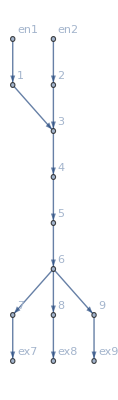

```mathematica
d2e["FG"]
```